```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\Code\\OutputData"];
```

## Модуль для отрисовки полученного решения PDE

```mathematica
PlotNPDE[data_] := Module[{plotdata},
plotdata =Manipulate[ListPlot[Table[{i-1, data[[t]][[i+1]]}, {i, 1, Length@data[[t]]-1}],PlotRange->Full, Mesh -> Full, Joined -> True(*, Filling->Bottom*),ColorFunction->"ThermometerColors", PlotStyle->{PointSize[Large]},AxesLabel->{"№","T, K"}], {t, 1, Length@data, 1} ];
plotdata
]
(*Аналитическое решение PDE *)
PDESolve[c_, rho_, L_, T_, k_, initfunc_, Gleft_, Gright_] := Module[{sol},
equ = c * rho * D[u[x, t], t] == D[(k[u[x,t], x]* D[u[x, t], x] ),x];
ic = {u[x, 0] == initfunc[x]};
bc ={u[0, t] == Gleft,  u[L, t] == Gright};
sol = DSolve [{equ, ic, bc}, u[x,t], {x, t}];
sol = sol[[1]][[1]][[2]];
(*sol = TruncateSum[sol, 100];*)
sol = sol/.K[1]->k;
sol
]
(* Модуль для отрисовки графика решения PDE*)
PDEPlot[sol_] := Module[{plotsol},
plotsol =Manipulate[Plot[Evaluate[sol/.{x->coord, t -> time}], {coord, 0, 1}] ,{time, 1, 100} ]

]
```

```mathematica
(* Рассмотрен тест 1: Алюминий, фикс. температура на концах*)

(* Получим аналитическое решение *)
c = 2600;
rho = 840;
h = 0.05;
L = 1;
tau = 0.009;
T = 100;
u0 = 800;

(*k[u_ , x_] = 237(1+0.0034(u-293));*)
k[u_, x_] = 221;
initfunc[x_] = u0-500-x(L-x);

Gleft =800;
Gright = 800;
sol =PDESolve[c, rho, L, T, k, initfunc,Gleft, Gright]
```

800+(4 (-1+(-1)^k) ⅇ^(-(17 k^2 π^2 t)/168000) (1+250 k^2 π^2) Sin[k π x])/(k^3 π^3)k1∞

```mathematica
sol2[x_,t_] =800+Sum[(4 (-1+(-1)^k) ⅇ^(-(17 k^2 π^2 t)/168000) (1+250 k^2 π^2) Sin[k π x])/(k^3 π^3), {k, 1, 50}];
```

```mathematica
(*Тест1: Алюминий,фиксированная температура на концах, K=const*)
test1 = Import["test1", "Table"];
(*PlotNPDE[test1]*)
```

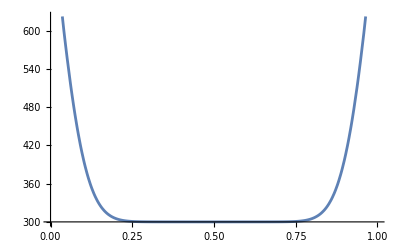

```mathematica
t = 30;
Show[Plot[sol2[x, t], {x, 0, 1}], ListPlot[Table[{i-1, test1[[t]][[i+1]]}, {i, 1, Length@test1[[t]]-1}],PlotRange->Full, Mesh -> Full, Joined -> True, ColorFunction->"ThermometerColors"]]
```